```mathematica
Cos[x]/Cos[n*x]^2 // Simplify
```

Cos[x] Sec[n x]^2

```mathematica
TrigReduce[Cos[x] Sec[n x]^2]
```

(2 Cos[x])/(1+Cos[2 n x])

```mathematica
Integrate[Exp[I*u]/Sqrt[Pi^2+E^2-2*E*Pi *Cos[u]],{u,0,2*Pi}]
```

(2 (ⅇ-π)^2 EllipticE[-(4 ⅇ π)/(ⅇ-π)^2]-2 (ⅇ^2+π^2) EllipticK[-(4 ⅇ π)/(ⅇ-π)^2])/(ⅇ (ⅇ-π) π)

```mathematica
Integrate[Exp[-I*u]/Sqrt[Pi^2+E^2-2*E*Pi *Cos[u]],{u,0,2*Pi}]
```

(2 (ⅇ-π)^2 EllipticE[-(4 ⅇ π)/(ⅇ-π)^2]-2 (ⅇ^2+π^2) EllipticK[-(4 ⅇ π)/(ⅇ-π)^2])/(ⅇ (ⅇ-π) π)

```mathematica
Integrate[Exp[0]/Sqrt[Pi^2+E^2-2*E*Pi *Cos[u]],{u,0,2*Pi}]
```

-(4 EllipticK[-(4 ⅇ π)/(ⅇ-π)^2])/(ⅇ-π)

```mathematica
Integrate[Exp[2*I*u]/Sqrt[Pi^2+E^2-2*E*Pi *Cos[u]],{u,0,2*Pi}]
```

$Aborted

```mathematica
N[Integrate[Exp[I*u]/Sqrt[Pi^2+E^2-2*E*Pi *Cos[u]],{u,0,2*Pi}]]
```

1.38652

```mathematica
N[Pi/E]
```

1.15573

```mathematica
Integrate[Cos[2*u]/Sqrt[Pi^2+E^2-2*E*Pi *Cos[u]],{u,0,2*Pi}]
```

(4 (ⅇ-π)^2 (ⅇ^2+π^2) EllipticE[-(4 ⅇ π)/(ⅇ-π)^2]-4 (ⅇ^4+ⅇ^2 π^2+π^4) EllipticK[-(4 ⅇ π)/(ⅇ-π)^2])/(3 ⅇ^2 (ⅇ-π) π^2)

```mathematica
Integrate[Cos[3*u]/Sqrt[Pi^2+E^2-2*E*Pi *Cos[u]],{u,0,2*Pi}]
```

1/(15 ⅇ^3 (ⅇ-π) π^3)(2 (ⅇ-π)^2 (8 ⅇ^4+7 ⅇ^2 π^2+8 π^4) EllipticE[-(4 ⅇ π)/(ⅇ-π)^2]-2 (8 ⅇ^6+7 ⅇ^4 π^2+7 ⅇ^2 π^4+8 π^6) EllipticK[-(4 ⅇ π)/(ⅇ-π)^2])

```mathematica
Integrate[Cos[n*u]/Sqrt[Pi^2+E^2-2*E*Pi *Cos[u]],{u,0,2*Pi}]
```

$Aborted

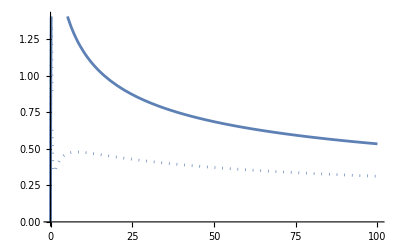

```mathematica
ReImPlot[LegendreQ[-1/2,(1+I*r^2)/(2*r)],{r,0,100}]
```

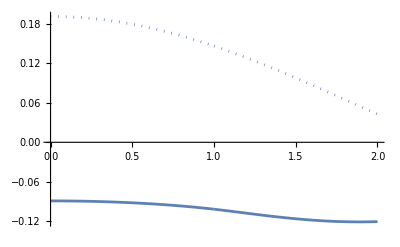

```mathematica
ReImPlot[Piecewise[{{I/4*HankelH1[0,r]*BesselJ[0,1]-1/(2*Pi)*BesselK[0,r]*BesselI[0,1],r>1},{I/4*HankelH1[0,1]*BesselJ[0,r]-1/(2*Pi)*BesselK[0,1]*BesselI[0,r],r<1}}],{r,0,2}]
```

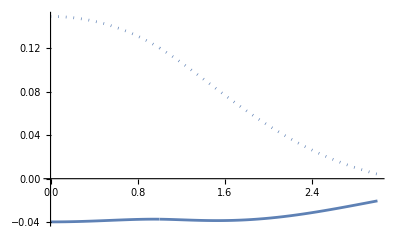

```mathematica
k = 1+0.5*I;
gf[r_] = Piecewise[{{I/4*HankelH1[0,k*r]*BesselJ[0,k*1]-1/(2*Pi)*BesselK[0,k*r]*BesselI[0,k*1],r>1},{I/4*HankelH1[0,k*1]*BesselJ[0,k*r]-1/(2*Pi)*BesselK[0,k*1]*BesselI[0,k*r],r<1}}];
ReImPlot[gf[r],{r,0,3}]
```

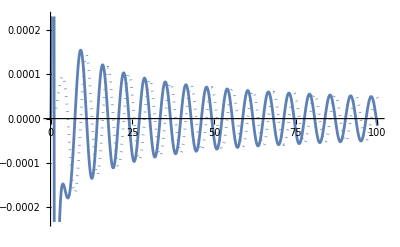

```mathematica
gfx[x_]=D[gf[x],x];
ReImPlot[gfx[r],{r,0,100}]
```

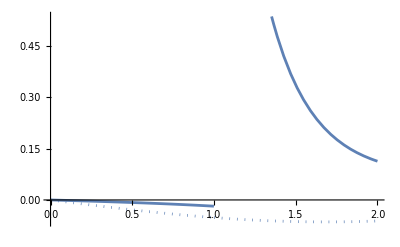

```mathematica
gf[r_] = Piecewise[{{I/4*HankelH1[0,r]*BesselJ[0,1]-1/(2*Pi)*BesselK[0,r]*BesselI[0,1],r>1},{I/4*HankelH1[0,1]*BesselJ[0,r]-1/(2*Pi)*BesselK[0,1]*BesselI[0,r],r<1}}];
gfxx[x_]=D[gf[x],{x,5}];
ReImPlot[gfxx[r],{r,0,2}]
```

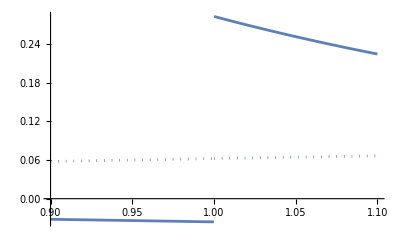

```mathematica
gfxxx[x_]=D[gfxx[x],x];
ReImPlot[gfxxx[r],{r,0.9,1.1}]
```

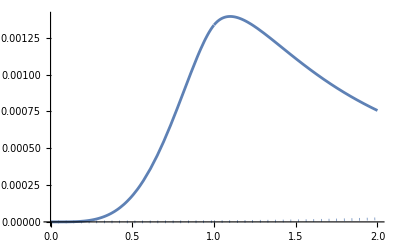

```mathematica
gf[r_] = Piecewise[{{I/4*HankelH1[4,r]*BesselJ[4,1]-1/(2*Pi)*BesselK[4,r]*BesselI[4,1],r>1},{I/4*HankelH1[4,1]*BesselJ[4,r]-1/(2*Pi)*BesselK[4,1]*BesselI[4,r],r<1}}];
gfx[x_]=D[gf[x],{x,0}];
ReImPlot[gfx[r],{r,0,2}]
```

```mathematica
D[Sqrt[x^2+y^2]^3,{x,3}]
```

-(3 x^3)/((x^2+y^2)^(3/2))+(9 x)/(√(x^2+y^2))

```mathematica
D[HankelH1[n,k*R],{R,3}] // Simplify
```

(k R (2+n^2-k^2 R^2) HankelH1[-1+n,k R]-(1+n) (2 n+n^2-k^2 R^2) HankelH1[n,k R])/R^3

```mathematica
D[BesselK[n,k*R],{R,3}] // Simplify
```

-(k R (2+n^2+k^2 R^2) BesselK[-1+n,k R]+(1+n) (2 n+n^2+k^2 R^2) BesselK[n,k R])/R^3

```mathematica
(D[HankelH1[0,k*Sqrt[x^2+y^2]],{x,2}]+D[HankelH1[0,k*Sqrt[x^2+y^2]],{y,2}] )// Simplify
```

1/2 k (-k HankelH1[0,k √(x^2+y^2)]-(2 HankelH1[1,k √(x^2+y^2)])/(√(x^2+y^2))+k HankelH1[2,k √(x^2+y^2)])

```mathematica
rhop = 4.4;
rho = 1.7;
NumberForm[1/Pi*Sqrt[rhop/rho]*LegendreQ[-1/2, (rho^2+rhop^2)/(2*rho*rhop)],12]
```

1.04081995178-0.761158009263 ⅈ

```mathematica
D[Exp[-R^2/(2s^2)],{R,3}]
```

-(ⅇ^(-R^2/(2 s^2)) R^3)/s^6+(3 ⅇ^(-R^2/(2 s^2)) R)/s^4

```mathematica
D[Exp[-R^2/(2s^2)],{R,3}]
```

-(ⅇ^(-R^2/(2 s^2)) R^3)/s^6+(3 ⅇ^(-R^2/(2 s^2)) R)/s^4

```mathematica
D[BesselJ[n,k*R],{R,3}] // Simplify
```

(k R (2+n^2-k^2 R^2) BesselJ[-1+n,k R]-(1+n) (2 n+n^2-k^2 R^2) BesselJ[n,k R])/R^3

```mathematica
D[BesselI[n,k*R],{R,3}] // Simplify
```

1/(2 R^3)(k R (2+n^2+k^2 R^2) BesselI[-1+n,k R]-2 (3 n^2+k^2 R^2) BesselI[n,k R]+k R (2+n^2+k^2 R^2) BesselI[1+n,k R])

```mathematica
x = 0.1;
y = 0.5;
theta = Pi/4;
StruveH[0,Sqrt[x^2+y^2+2*x*y*Cos[theta]]]
```

0.352828

```mathematica
Sum[StruveH[n,x]*BesselJ[-n,y]*Exp[I*n*theta],{n,-10,10}]
```

683.852+4819.9 ⅈ

```mathematica
x = 1;
xpp = -2;
k = 1+I;
NIntegrate[Log[Abs[x-xp]]*Exp[I*k*Abs[xp-xpp]],{xp,-Infinity,Infinity}]
```

1.22491+0.972297 ⅈ

```mathematica
x = 1;
xpp = -2;
k = 1+I;
NIntegrate[Log[Abs[xp-xpp]]*Exp[I*k*Abs[x-xp]],{xp,-Infinity,Infinity}]
```

1.22491+0.972297 ⅈ

```mathematica
1-(40/52)^3
```

1197/2197

```mathematica
N[1197/2197]
```

0.544834

```mathematica
1-(40/52)*(39/51)*(38/50)
```

47/85

```mathematica
N[47/85]
```

0.552941

```mathematica
2*Binomial[8,4]/Binomial[10,5]
```

5/9